```mathematica
Sum[x^(n*r+k)/(n*r+k)(-1)^(n*r),{n,0,Infinity}]//Simplify(* узнаю чему равен ряд такого вида *)
```

(x^k Hypergeometric2F1[1,k/r,(k+r)/r,(-1)^r x^r])/k

```mathematica
F[z_,x_]:=Sum[(-ProductLog[-x])^k GCD[k,z] Hypergeometric2F1[1,k/z,k/z+1,(-ProductLog[-x])^z]/k,{k,1,z}] (*задаю функцию F из курсовой*)
```

```mathematica
F1[z_,x_]:=F[z,x]/(1+ProductLog[-x])(*получаю непосредственую функцию для подсчетов получившегося числа компонент для отображений обладающих одной компонентой *)
```

```mathematica
k=50;
ls=Table[SeriesCoefficient[F1[3,x],{x,0,i}]*(i!)/i^i,{i,1,k}];(*тут получаю среднее количество распавшихся компонент для алфавитов разных мощностей *)
```

```mathematica
ls//N
```

{1.,1.25,1.40741,1.52344,1.61568,1.69239,1.75812,1.81567,1.86688,1.91303,1.95504,1.9936,2.02925,2.06239,2.09336,2.12244,2.14984,2.17574,2.20031,2.22368,2.24596,2.26724,2.28762,2.30716,2.32595,2.34402,2.36144,2.37825,2.39449,2.4102,2.42541,2.44016,2.45447,2.46837,2.48188,2.49502,2.50782,2.52028,2.53243,2.54428,2.55585,2.56715,2.5782,2.58899,2.59955,2.60989,2.62001,2.62992,2.63964,2.64916,2.6585,2.66767,2.67666,2.68549,2.69417,2.70269,2.71106,2.7193,2.72739,2.73536,2.7432,2.75091,2.7585,2.76597,2.77334,2.78059,2.78773,2.79478,2.80172,2.80857,2.81532,2.82198,2.82854,2.83503,2.84142,2.84774,2.85397,2.86012,2.8662,2.87221,2.87814,2.884,2.88979,2.89551,2.90117,2.90676,2.91228,2.91775,2.92316,2.9285,2.93379,2.93903,2.9442,2.94933,2.9544,2.95941,2.96438,2.9693,2.97417,2.97899}

```mathematica
Table[ls[[i]]*i^i,{i,1,10}](*а тут просто их количество суммарное *)
```

{1,5,42,454,6049,96480,1795786,38231984,916608825,24442338880}

```mathematica
line=Fit[ls,{1,Log[x]},x] (*смотрю какой вид имеет приближающая их функция*)
```

0.925422+0.436483 Log[x]

```mathematica
m=1000
ls = Table[Sum[(HarmonicNumber[x] x n!)/((n-x)! n^(x+1)),{x,1,n}],{n,1,m}] (*тут эти значение полученные с помощью непосредственной формулы, в случае, когда итерация только одна*)
```

1000

{1,998,(22165197183684643568179503398715372185743446653958027401361676157724711524121079932559187592525860455705115569850801469217733765055354783894967078047828348638391199541376705707031438704806287552976242665399150025119405956127703020749234339638278720078042483796928594269927201687819778394101273178305137872195542395241472066649806741145992348414762201082901501425866497061382445166852681285807083501467486916140030073417534972404046323376165926707445886433972021)/(54032272097832669246459784228451983075981138608015016656103911644943714500114771327537297823159345375717368526218768598561674208547987731877373806351344227840281947721670536364864508851292023346734825914127219669307526152094961120730000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)}
 |  |  |  |

```mathematica
plot=Show[Plot[(Log[2x]+EulerGamma)/2,{x,1,1000},PlotStyle->{Thickness[0.005],Black},LabelStyle->Directive[20],AxesLabel->{"n"},GridLines->Automatic],ListPlot[Labeled[ls,"Точное значение"],PlotStyle->{Red,PointSize[Medium]}]](*аппроксимация этих чисел с помощью нашей функции *)
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]; (* выгрузка графика *)
SetDirectory["./images"];
Export["Comp1.jpg",plot,ImageSize->1024];
```

```mathematica
z=4;
n=11;
k=10;
SeriesCoefficient[1/((k-1)!)F[z,x](F[1,x])^(k-1),{x,0,n}]*n! (* функция для поулчения основных искомых чисел *)
```

1705

```mathematica
Clear[n,k,x,r]
Sum[x^{n*r+k}/(n*r+k),{n,0,Infinity}] (*определяем функцию имеющую соответствующий ряд*)
```

{(x^k HurwitzLerchPhi[x^r,1,k/r])/r}

```mathematica
Fb[r_,x_]:=Sum[GCD[k,r]x^k HurwitzLerchPhi[x^r,1,k/r]/r,{k,1,r}] (*задаю функцию Fb из курсовой*)
```

```mathematica
Fbc[z_,n_]:= SeriesCoefficient[Fb[z,x]/(1-x),{x,0,n}]n! (* функция для получения необходимых чисел в случае биективного отображения *)
```

```mathematica
ls = Table[ Sum[(k+1)^2(n^(-k-2)n!)/((n-k-1)!),{k,0,n-1}],{n,1,m}](* список среднего максимально возможного числа компонент в результате итерации случаеного отображения над алфавита мощности n, полученных с помощью непосредственной формулы *)
```

{1,998,(2123641895146312196759432117239562444736654637476230155627804460708861906013968239974398749255319907274199322530982204496272180688259931581351374997266180482659897102163624727845932036009541631023200666298091974322710905845910743255703762708198772880116406769937784392661456465174962608134469460292746403436578520174715152081656455885645968577377836567348109592570851893059537932948829303426217808548656059264054899700791467738088134204351018974788249971481636517974254159034690824142116572413548631370236007190531134368779650417570818078251879701876048943977162393919185156655023592071072523940718035565091267055556358780507811437088951103289414747725953571172858449478220080825308443716876740594296600100003254456783607894742260635254914829888055256483320277190104071131361670928348435000344128376255849928817899727397532669065003043725687466379566363593848539486485533329331602187780597730668084437247961676673295439779056272267829187493021)/(5403227209783266924645978422845198307598113860801501665610391164494371450011477132753729782315934537571736852621876859856167420854798773187737380635134422784028194772167053636486450885129202334673482591412721966930752615209496116652660235285528239001760654282794458314926664629658296287156392117744634388955610504325881746857069529444540181100058305397601335078884774853982709410535301204045320559316422385605854296471928467449220338419616144024596229587413008286251776158800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)}
 |  |  |  |

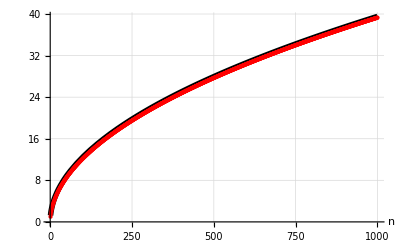

```mathematica
plot = Show[Plot[5/4 √x,{x,1,1000},PlotStyle->{Black,Thickness[0.01]},LabelStyle->Directive[20],AxesLabel->{"n"},GridLines->Automatic],ListPlot[ls,PlotStyle->{Red,PointSize[Medium]}]] (* график показывающий аппроксимацию и снизу его выгрузка *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["./images"];
Export["Comp2.jpg",plot,ImageSize->1024];
```